```mathematica
(*
Don't really know how to reduce this

I thought about switching to a 6-d model, since we don't really need to differentiate between old males and young males right, since they can reproduce regardless?
*)

Z = Subscript[m, 1][t]+Subscript[M, 1][t] + Subscript[m, 2][t]+Subscript[M, 2][t];
 (*Young males with trait 1*)          b*(1/Z)*(Subscript[r, 1] Subscript[f, 1][t](Subscript[m, 1][t]+Subscript[M, 1][t]) + (1/2)*Subscript[r, 1] Subscript[f, 1][t]*(Subscript[m, 2][t]+Subscript[M, 2][t]) + (1/2)*(Subscript[r, 2] Subscript[f, 2][t]*(Subscript[m, 1][t]+Subscript[M, 1][t])))- Subscript[α, 1] Subscript[m, 1][t];
(*Mature males with trait 1*)         Subscript[α, 1] Subscript[m, 1][t];
(*Young females with trait 1*)       b*(1/Z)*((1-Subscript[r, 1])*Subscript[f, 1][t](Subscript[m, 1][t]+Subscript[M, 1][t]) + (1/2)*(1-Subscript[r, 1])*Subscript[f, 1][t]*(Subscript[m, 2][t]+Subscript[M, 2][t]) + (1/2)*((1-Subscript[r, 2])*Subscript[f, 2][t]*(Subscript[m, 1][t]+Subscript[M, 1][t])))- Subscript[α, 2] Subscript[f, 1][t];
(*Mature females with trait 1*)     Subscript[α, 2] Subscript[f, 1][t];
(*Young males with trait 2*)            b*(1/Z)*(Subscript[r, 2] Subscript[f, 2][t](Subscript[m, 2][t]+Subscript[M, 2][t]) + (1/2)*Subscript[r, 1] Subscript[f, 1][t]*(Subscript[m, 2][t]+Subscript[M, 2][t]) + (1/2)*(Subscript[r, 2] Subscript[f, 2][t]*(Subscript[m, 1][t]+Subscript[M, 1][t])))- Subscript[α, 1] Subscript[m, 2][t];
(*Mature males with trait 2*)           Subscript[α, 1] Subscript[m, 2][t];
(*Young females with trait 2*)        b*(1/Z)*((1-Subscript[r, 2])*Subscript[f, 2][t](Subscript[m, 2][t]+Subscript[M, 2][t]) + (1/2)*(1-Subscript[r, 1])*Subscript[f, 1][t]*(Subscript[m, 2][t]+Subscript[M, 2][t]) + (1/2)*((1-Subscript[r, 2])*Subscript[f, 2][t]*(Subscript[m, 1][t]+Subscript[M, 1][t])))- Subscript[α, 2] Subscript[f, 2][t];
(*Mature females with trait 2*)      Subscript[α, 2] Subscript[f, 2][t];

b = 1;
Subscript[α, 1] = 0;
Subscript[α, 2] = 1;
Subscript[r, 1] = (1/2);
Subscript[r, 2] = (1/2);
tmax = 10^4;
sol:=NDSolve[{Subscript[m, 1]'[t] ==  b*(1/Z)*(Subscript[r, 1] Subscript[f, 1][t](Subscript[m, 1][t]+Subscript[M, 1][t]) + (1/2)*Subscript[r, 1] Subscript[f, 1][t]*(Subscript[m, 2][t]+Subscript[M, 2][t]) + (1/2)*(Subscript[r, 2] Subscript[f, 2][t]*(Subscript[m, 1][t]+Subscript[M, 1][t])))- Subscript[α, 1] Subscript[m, 1][t], Subscript[M, 1]'[t] == Subscript[α, 1] Subscript[m, 1][t], Subscript[f, 1]'[t] == b*(1/Z)*((1-Subscript[r, 1])*Subscript[f, 1][t](Subscript[m, 1][t]+Subscript[M, 1][t]) + (1/2)*(1-Subscript[r, 1])*Subscript[f, 1][t]*(Subscript[m, 2][t]+Subscript[M, 2][t]) + (1/2)*((1-Subscript[r, 2])*Subscript[f, 2][t]*(Subscript[m, 1][t]+Subscript[M, 1][t])))- Subscript[α, 2] Subscript[f, 1][t],Subscript[F, 1]'[t] ==Subscript[α, 2] Subscript[f, 1][t], Subscript[m, 2]'[t] == b*(1/Z)*(Subscript[r, 2] Subscript[f, 2][t](Subscript[m, 2][t]+Subscript[M, 2][t]) + (1/2)*Subscript[r, 1] Subscript[f, 1][t]*(Subscript[m, 2][t]+Subscript[M, 2][t]) + (1/2)*(Subscript[r, 2] Subscript[f, 2][t]*(Subscript[m, 1][t]+Subscript[M, 1][t])))- Subscript[α, 1] Subscript[m, 2][t], Subscript[M, 2]'[t] == Subscript[α, 1] Subscript[m, 2][t],Subscript[f, 2]'[t] ==b*(1/Z)*((1-Subscript[r, 2])*Subscript[f, 2][t](Subscript[m, 2][t]+Subscript[M, 2][t]) + (1/2)*(1-Subscript[r, 1])*Subscript[f, 1][t]*(Subscript[m, 2][t]+Subscript[M, 2][t]) + (1/2)*((1-Subscript[r, 2])*Subscript[f, 2][t]*(Subscript[m, 1][t]+Subscript[M, 1][t])))- Subscript[α, 2] Subscript[f, 2][t], Subscript[F, 2]'[t]== Subscript[α, 2] Subscript[f, 2][t],Subscript[m, 1][0] ==1,Subscript[M, 1][0] ==1, Subscript[f, 1][0] == 1, Subscript[F, 1][0] ==1,Subscript[m, 2][0] == 1, Subscript[M, 2][0] ==1, Subscript[f, 2][0] ==1,Subscript[F, 2][0]== 1},{Subscript[m, 1],Subscript[M, 1],Subscript[f, 1],Subscript[F, 1],Subscript[f, 2],Subscript[F, 2],Subscript[m, 2],Subscript[M, 2]} ,{t,0,tmax}];
```

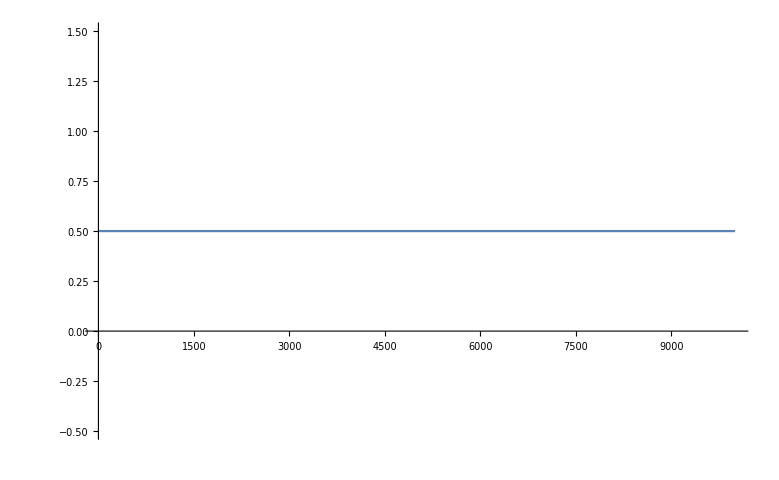

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of (1/10 f_1 (m_1+M_1)+1/10 f_2 (m_1+M_1)+1/20 f_1 (m_2+M_2))/M.

```mathematica
Plot[Evaluate[{(Subscript[m, 1][t]+Subscript[M, 1][t]+Subscript[f, 1][t] + Subscript[F, 1][t])/(Subscript[m, 1][t]+Subscript[M, 1][t] + Subscript[f, 1][t] + Subscript[F, 1][t] + Subscript[f, 2][t] + Subscript[F, 2][t] + Subscript[m, 2][t] + Subscript[M, 2][t])}/.sol],{t,0,tmax},PlotRange -> All]
```